# 水滴

### 构造曲线

我们先来画一个圆



```mathematica
ParametricPlot[{Cos[v],Sin[v]},{v,0,2π}]
```

然后对y轴进行变形，加上变量v，使其向上偏移

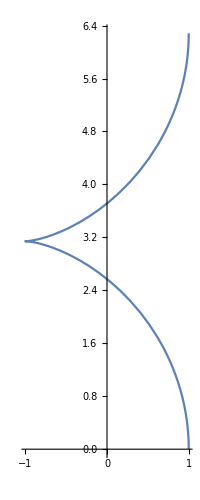

```mathematica
ParametricPlot[{Cos[v],Sin[v]+v},{v,0,2π}]
```

我们试试减小上一步对y轴的改变

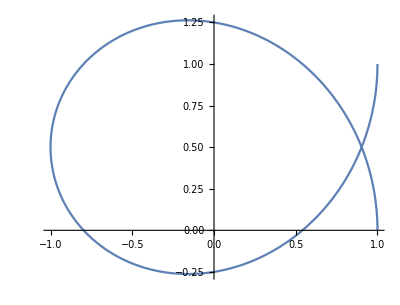

```mathematica
ParametricPlot[{Cos[v],Sin[v]+v/(2π)},{v,0,2π}]
```

这下有水滴的样子了，将其向下平移0.5，对齐到原点

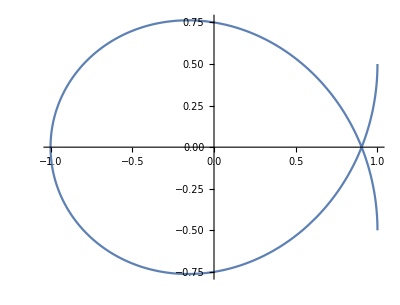

```mathematica
ParametricPlot[{Cos[v],Sin[v]+v/(2π)-0.5},{v,0,2π}]
```

再修剪一下，
先计算上图的交点对应的v值，需要注意条件0<v<2π是必要的，否则Mathematica无法求解

```mathematica
Solve[{Sin[v]+v/(2π)==1/2,0<v<2π}]
```

{{v→π},{v→Root0.444Root[{-π+2 π Sin[#1]+#1&,0.443793032386938846011}]0.44379303238693885},{v→Root5.84Root[{-π+2 π Sin[#1]+#1&,5.8393922747926476309}]5.839392274792647}}

修改变量v的开始和结束

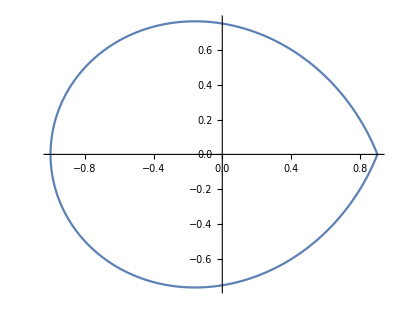

```mathematica
ParametricPlot[{Cos[v],Sin[v]+v/(2π)-0.5},{v,0.444,5.84}]
```

交换x和y轴，让它立起来，就能得到水滴曲线

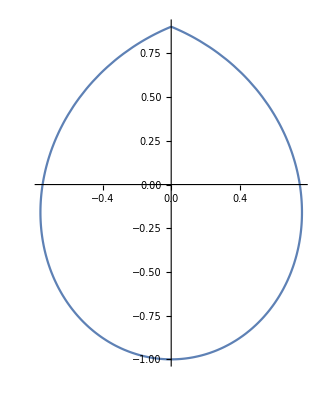

```mathematica
ParametricPlot[{Sin[v]+v/(2π)-0.5,Cos[v]},{v,0.444,5.84}]
```

好啦，基本准备就绪

### 绘制3D图形

接下来只需将曲线绕y轴旋转一下就能得到一个3D的水滴，
略微注意下v的取值范围

```mathematica
RevolutionPlot3D[{Sin[v]+v/(2π)-0.5,Cos[v]},{v,0.444,π},RotationAction->"Clip"]
```

-Graphics3D-

当然使用ParametricPlot3D也是可以的

```mathematica
ParametricPlot3D[{Cos[u](Sin[v]+v/(2π)-0.5),Sin[u](Sin[v]+v/(2π)-0.5),Cos[v]},{u,0,2π},{v,0.444,π},RotationAction->"Clip"]
```

-Graphics3D-

### 给水滴上色

```mathematica
RevolutionPlot3D[{Sin[v]+v/(2π)-0.5,Cos[v]},{v,0.444,π},RotationAction->"Clip",MeshShading->{{Red, Yellow}, {Pink, Orange}}]
```

-Graphics3D-

彩虹水滴

```mathematica
RevolutionPlot3D[{Sin[v]+v/(2π)-0.5,Cos[v]},{v,0.444,π},RotationAction->"Clip",ColorFunction->"Rainbow",Mesh->None]
```

-Graphics3D-

金色水滴

```mathematica
RevolutionPlot3D[{Sin[v]+v/(2π)-0.5,Cos[v]},{v,0.444,π},RotationAction->"Clip",Mesh->None,PlotStyle->MaterialShading["Gold"],Lighting->"ThreePoint"]
```

-Graphics3D-

素描风格

```mathematica
RevolutionPlot3D[{Sin[v]+v/(2π)-0.5,Cos[v]},{v,0.444,π},RotationAction->"Clip",Mesh->None,PlotStyle->Directive[GrayLevel[0.77],HatchShading[]],Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[{Sin[v]+v/(2π)-0.5,Cos[v]},{v,0.444,π},RotationAction->"Clip",Mesh->None,PlotPoints->40,PlotStyle->Directive[GrayLevel[0.77],ToonShading[]],Lighting->"Neutral"]
```

-Graphics3D-

水滴本滴

```mathematica
RevolutionPlot3D[{Sin[v]+v/(2π)-0.5,Cos[v]},{v,0.444,π},RotationAction->"Clip",Mesh->None,PlotPoints->40,PlotStyle->Directive[MaterialShading[<|"BaseColor"-> GrayLevel[0.92, 0.56],"RoughnessCoefficient"-> 0.25,"SheenColor"-> GrayLevel[1, 0.36],"SheenRoughnessCoefficient"->0.2|>]],Lighting->"ThreePoint",Axes->False,Boxed->False]
```

-Graphics3D-

```mathematica
RevolutionPlot3D[{Sin[v]+v/(2π)-0.5,Cos[v]},{v,0.444,π},RotationAction->"Clip",Mesh->None,PlotStyle->Directive[White,MaterialShading[<|"BaseColor"-> GrayLevel[1, 0.56],"SurfaceNormals"-> Texture[-Graphics-],
"SheenColor"->RGBColor[1, 1, 1, 0.87],"RoughnessCoefficient"-> 0.5, "SpecularColor"-> GrayLevel[1, 0.85]|>]],Lighting->"ThreePoint"]
```

-Graphics3D-

## Over！